<|"Title"→"Playing with YouTube from Mathematica",
"Date":>"Fri 28 Sep 2018 19:45:03""GMT"-7.,"Modified":>Now,"Tags"→{},"Slug"→Automatic,"Authors"→{}|>

Today I’m gonna quickly show off something I made for a friend (and about which I’d been thinking for some time). We’re gonna use the YouTube API in Mathematica to do a have some fun (but not too much fun, mind you!).

#### Installing the YouTube Connection

My connection to the YouTube API is built on Mathematica’s ServiceConnect framework. I’ve talked about these before in many different contexts but today we’ll just use it. To install we pull the paclet off my server:

```mathematica
PacletInstall["ServiceConnection_YouTube",
	"Site"->
		"http://www.wolframcloud.com/objects/b3m2a1.paclets/PacletServer/"
	]
```

Paclet[…]

#### Authenticating with YouTube

One installed, we connect to the service as usual:

```mathematica
$so = ServiceConnect["YouTube"]
```

This will open a dialog:

-Graphics-

We’ll click the sign in button, pick and account (I’ll use my new personal account steve.wolfraum@gmail.com):

-Graphics-

When we click “Allow” either we’ll be taken to a nicely formatted local page with an access code running via HTTPHandling`StartWebServer or if that’s being glitchy as it was right now, we’ll copy the part of the URL starting with "code=4/...":

-Graphics-

Finally, we’re connected:

ServiceObject[…]

#### Getting Data

The majority of the currently supported methods have to do with getting data about YouTube:

```mathematica
$so["Requests"]
```

{Authentication,DeleteVideo,ID,Information,LastRequest,ListCaptions,ListChannelActivity,ListChannels,ListChannelSections,ListComments,ListCommentThreads,ListPlaylistItems,ListPlaylists,ListSubscriptions,ListVideos,Name,RawRequests,RequestData,RequestParameters,Search,UpdateVideo,UploadVideo,VideoURL}

We’ll start with a search, maybe. First let’s see what parameters we have to work with:

```mathematica
$so["RequestParameters", "Request"->"Search"]
```

<|Parameters→{q,part,forContentOwner,forDeveloper,forMine,relatedToVideoId,channelId,channelType,eventType,location,locationRadius,maxResults,onBehalfOfContentOwner,order,pageToken,publishedAfter,publishedBefore,q,regionCode,relevanceLanguage,safeSearch,topicId,type,videoCaption,videoCategoryId,videoDefinition,videoDimension,videoDuration,videoEmbeddable,videoLicense,videoSyndicated,videoType},Required→{part}|>

Then we’ll search for something bland, like “Steve Wolfraum”. The YouTube API requires this "part" parameter to know what to return to use. I like to get the "id" and "snippet" parts, but you can pick for yourself which parts you want. Just comma-separate your values and you can get multiple different ones:

```mathematica
mySearch = $so["Search", "q"->"Steve Wolfraum", "part"->"id,snippet"]
```

Dataset[<>]

We see there are tons of results for “my” name but we only get them five at a time. We can use the "nextPageToken" to get the next page of results, though. We can bump up the number we get with the "maxResults" parameter, but I see no need for that right now. Let’s look at the first result here. I’ll drill straight into that snippet parameter, as that’s the most interesting part:

```mathematica
mySearch["items", 1, "snippet"]
```

Dataset[<>]

And we see, sadly, that instead of getting results for my name, Steve Wolfraum, we get them for some random dude name Stephen Wolfram. Not to be deterred, let’s at least get something out of this and see a thumbnail for all our results. Tragically, we can’t download videos with the YouTube API, but at least we get thumbnails...hooray? To make things more fun, we’ll also add a filter to all these results, as the raw thumbnails really aren’t all that interesting.

```mathematica
ImageAdjust@LaplacianGaussianFilter[Import[#], 3]&/@
	Normal@mySearch["items", All, "snippet", "thumbnails", "high", "url"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Cool. There’s some data. We can also pull out statistics and things, say for different videos broadcast on the Wolfram Research channel. First we’ll get their channel ID:

```mathematica
wriChannel=
	$so["Search", "q"->"Wolfram Research", "type"->"channel",
		"part"->"id", "maxResults"->"1"]["items", 1, "id", "channelId"]
```

UCJekgf6k62CQHdENWf2NgAQ

Now we’ll use this to extract the 50 most popular videos:

```mathematica
wriVids=$so["Search", "channelId"->wriChannel, "type"->"video", 
	"order"->"viewCount", "part"->"id,snippet", "maxResults"->"50"]
```

Dataset[<>]

And now we’ll get view counts:

```mathematica
wriStats=$so["ListVideos", 
	"id"->StringRiffle[Normal@wriVids["items", All, "id", "videoId"], ","], 
	"part"->"statistics"
	]
```

Dataset[<>]

And then we’ll make a WordCloud of titles vs viewcounts:

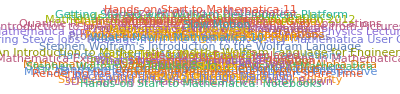

```mathematica
WordCloud@
	AssociationThread[
		Normal@wriVids["items", All, "snippet", "title"],
		ToExpression@Normal@wriStats["items", All, "statistics", "viewCount"]
		]
```

And we see as far as YouTube cares, there’s really only one video WRI has made. But dropping that one we might see some more interesting structure:

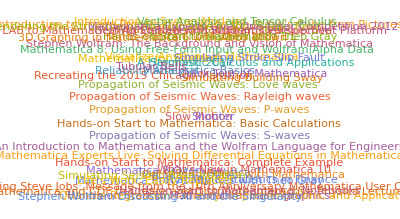

```mathematica
WordCloud@
	AssociationThread[
		Rest@Normal@wriVids["items", All, "snippet", "title"],
		Rest@ToExpression@Normal@wriStats["items", All, "statistics", "viewCount"]
		]
```

And it seems that people really like the basics and...really like seismic waves?

I’ll embed the first of those so we can see how good the really are:

```mathematica
$so["EmbedIFrame", "id"->wriVids["items", 3, "id", "videoId"]]
```

Null<iframe id="ytplayer" type="text/html" wi…U4?autoplay=0"
  frameborder="0"></iframe><iframe id="ytplayer" type="text/html" width="640" height="360"
src="https://www.youtube.com/embed/2rYjlVPU9U4?autoplay=0"
  frameborder="0"></iframe>

#### Uploading Videos

A YouTube API wouldn’t be much of a YouTube API if it couldn’t upload videos, of course, so I cooked that in as well.

Here’s a sample of that. We’ll first pull an animation off the Manipulate docs:

```mathematica
anim =
	Export[
		FileNameJoin@{$TemporaryDirectory, "plot3d.flv"},
		Manipulate[
			Plot3D[Sin[n x y], 
				{x, 0, 3}, {y, 0, 3}, 
				ViewPoint -> Dynamic[{2, v, 2}], SphericalRegion -> True, Ticks -> None,
				PerformanceGoal->"Quality"
				], 
			{n, 1, 4}, 
			{v, -2, 2}
			]
		];
```

Then we’ll upload the video we made:

```mathematica
upload = $so["UploadVideo", "part"->"id", "BodyContent"->anim];
```

Then we attach a title and things in a second request:

```mathematica
$so["UpdateVideo", "id" -> upload["id"],
 "part" -> "snippet",
  "Title" -> "Mathematica Examples: Plot 3D",
 "CategoryID" -> "22"
 ]
```

Dataset[<>]

And then now we’ll embed that video we just made:

```mathematica
$so["EmbedIFrame", "id"->upload["id"]]
```

Null<iframe id="ytplayer" type="text/html" wi…_Q?autoplay=0"
  frameborder="0"></iframe><iframe id="ytplayer" type="text/html" width="640" height="360"
src="https://www.youtube.com/embed/Quzcr4Vuq_Q?autoplay=0"
  frameborder="0"></iframe>